# Fits with Cu d-Hamiltonian

```mathematica
Needs["GroupTheory`"];
```

```mathematica
dir=NotebookDirectory[];
```

```mathematica
SetDirectory[dir];
```

## d-Hamiltonian

Read the Hamiltonian from file

```mathematica
hfcc=GTReadFromFile["fcc_d.ham"];
```

## Parameters

```mathematica
cu=GTReadFromFile["parm0.parm"]
```

{{(ddσ)_1,-0.02566},{(ddπ)_1,0.018},{(ddδ)_1,-0.00408},{(ddσ)_2,-0.00451},{(ddπ)_2,0.00241},{(ddδ)_2,-0.00029},{(dd0),0.37}}

```mathematica
cu1=GTReadFromFile["parm1.parm"]
```

{{(ddσ)_1,-0.0320611},{(ddπ)_1,0.0229274},{(ddδ)_1,-0.0176965},{(ddσ)_2,-0.00965185},{(ddπ)_2,-0.00707285},{(ddδ)_2,0.0177796},{(dd0),0.380387}}

## Band structure

parametrize Hamiltonian

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu];
```

calculate band structure

Maximum Abscissa = 4.48735

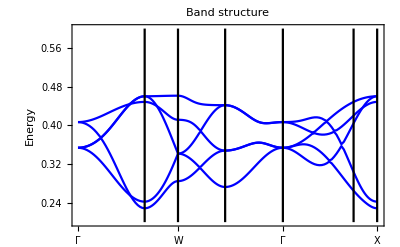

```mathematica
kp=GTBZPath["fcc"];
plt1=GTBandStructure[hfccp,kp,30,5, Joined->True,PlotStyle->Blue,PlotRange->{{0,4.5},{.2,.6}}]
```

parametrize Hamiltonian

```mathematica
hfccp= hfcc /. GTTbParmToRule[cu1];
```

calculate band structure

Maximum Abscissa = 4.48735

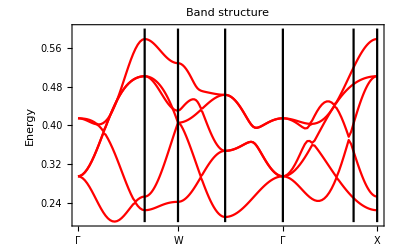

```mathematica
kp=GTBZPath["fcc"];
plt2=GTBandStructure[hfccp,kp,30,5, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{.2,.6}}]
```

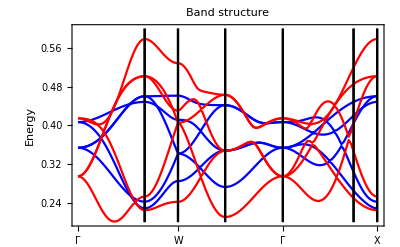

```mathematica
Show[plt1,plt2]
```

## Least Squares

```mathematica
SetDirectory[dir<>"../fit/lsqr"];
```

### Test the fit at the points

```mathematica
pfit=GTTbParmImport["dn1sf.parm",cu]
```

{{(ddσ)_1,-0.0246968},{(ddπ)_1,0.0181825},{(ddδ)_1,-0.00474409},{(ddσ)_2,-0.00887849},{(ddπ)_2,-0.00134588},{(ddδ)_2,0.00565014},{(dd0),0.37}}

```mathematica
hfccp= hfcc /. GTTbParmToRule[pfit];
```

calculate band structure

Maximum Abscissa = 4.48735

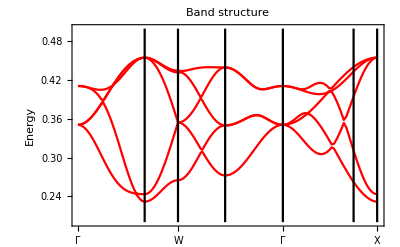

```mathematica
kp=GTBZPath["fcc"];
plt2=GTBandStructure[hfccp,kp,30,5, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{.2,.5}}]
```

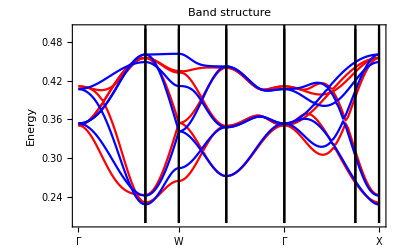

```mathematica
Show[plt2,plt1]
```

### Test the fit along the lines

```mathematica
pfit1=GTTbParmImport["dn1sf2.parm",cu]
```

{{(ddσ)_1,-0.02566},{(ddπ)_1,0.018},{(ddδ)_1,-0.00408},{(ddσ)_2,-0.00451},{(ddπ)_2,0.00241},{(ddδ)_2,-0.00029},{(dd0),0.37}}

```mathematica
hfccp= hfcc /. GTTbParmToRule[pfit1];
```

Maximum Abscissa = 4.48735

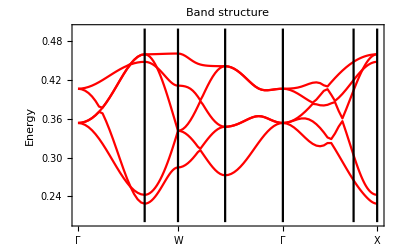

```mathematica
kp=GTBZPath["fcc"];
plt3=GTBandStructure[hfccp,kp,20,5, Joined->True,PlotStyle->{{Red,PointSize[.3]}},PlotRange->{{0,4.5},{.2,.5}}]
```

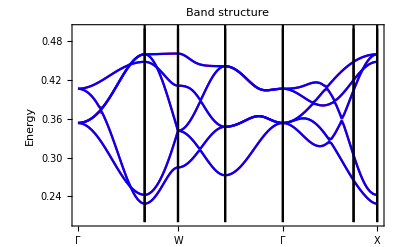

```mathematica
Show[plt3,plt1]
```

### Test second neighbor parameters set to zero

```mathematica
pfit2=GTTbParmImport["df3.parm",cu]
```

{{(ddσ)_1,-0.0256659},{(ddπ)_1,0.0182205},{(ddδ)_1,-0.00430534},{(ddσ)_2,0.},{(ddπ)_2,0.},{(ddδ)_2,0.},{(dd0),0.369889}}

```mathematica
hfccp= hfcc /. GTTbParmToRule[pfit2];
```

Maximum Abscissa = 4.48735

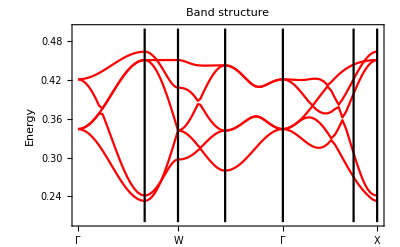

```mathematica
kp=GTBZPath["fcc"];
plt4=GTBandStructure[hfccp,kp,20,5, Joined->True,PlotStyle->{{Red,PointSize[.3]}},PlotRange->{{0,4.5},{.2,.5}}]
```

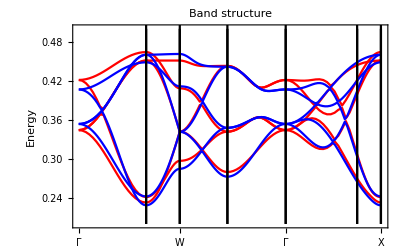

```mathematica
Show[plt4,plt1]
```

#### Take now all parameters

```mathematica
pfit3=GTTbParmImport["df4.parm",cu]
```

{{(ddσ)_1,-0.02566},{(ddπ)_1,0.018},{(ddδ)_1,-0.00408},{(ddσ)_2,-0.00451},{(ddπ)_2,0.00241},{(ddδ)_2,-0.00029},{(dd0),0.37}}

```mathematica
hfccp= hfcc /. GTTbParmToRule[pfit3];
```

```mathematica
kp=GTBZPath["fcc"];
plt5=GTBandStructure[hfccp,kp,20,5, Joined->True,PlotStyle->{{Red,PointSize[.3]}},PlotRange->{{0,4.5},{.2,.5}}]
```

Maximum Abscissa = 4.48735

-Graphics-

```mathematica
Show[plt5,plt1]
```

-Graphics-

## Genetic algorithm

```mathematica
SetDirectory[dir<>"../fit/genalg"];
```

```mathematica
pg=GTTbParmImport["genf1.parm",cu]
```

{{(ddσ)_1,-0.0255491},{(ddπ)_1,0.0180594},{(ddδ)_1,-0.0041927},{(ddσ)_2,-0.00370001},{(ddπ)_2,0.0028},{(ddδ)_2,-0.0011013},{(dd0),0.37002}}

```mathematica
hfccp= hfcc /. GTTbParmToRule[pg];
```

calculate band structure

Maximum Abscissa = 4.48735

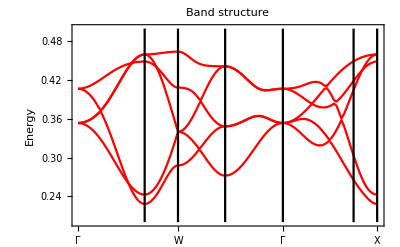

```mathematica
kp=GTBZPath["fcc"];
pltg1=GTBandStructure[hfccp,kp,30,5, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{.2,.5}}]
```

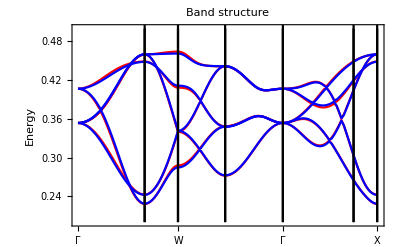

```mathematica
Show[pltg1,plt1]
```

## Simplex method

```mathematica
SetDirectory[dir<>"../fit/simplex"];
```

### Band structure with noisy parameters

Read the parameters with noise in range [-0.05,+0.05]

```mathematica
pg=GTTbParmImport["parm_0.parm",cu]
```

{{(ddσ)_1,0.015933},{(ddπ)_1,0.0401467},{(ddδ)_1,0.00480893},{(ddσ)_2,0.0178104},{(ddπ)_2,-0.0264219},{(ddδ)_2,-0.0348536},{(dd0),0.384749}}

Plot the band structure

Maximum Abscissa = 4.48735

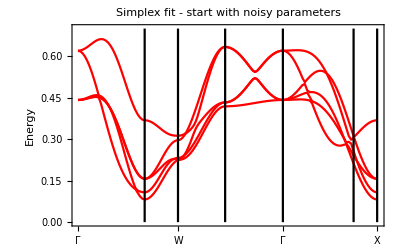

```mathematica
hfccp= hfcc /. GTTbParmToRule[pg];
kp=GTBZPath["fcc"];
simp0=GTBandStructure[hfccp,kp,30,5, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{0,.7}},PlotLabel->"Simplex fit - start with noisy parameters"]
```

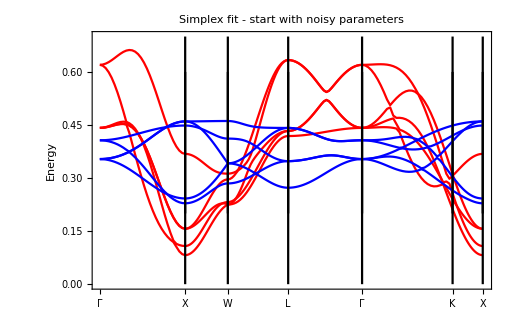

```mathematica
Show[simp0,plt1]
```

### Fit with symmetry points only

```mathematica
pg=GTTbParmImport["cu_syf.parm",cu]
```

{{(ddσ)_1,-0.0256598},{(ddπ)_1,0.0179999},{(ddδ)_1,-0.00407991},{(ddσ)_2,-0.00450932},{(ddπ)_2,0.00240988},{(ddδ)_2,-0.000290333},{(dd0),0.369999}}

```mathematica
hfccp= hfcc /. GTTbParmToRule[pg];
```

calculate band structure

Maximum Abscissa = 4.48735

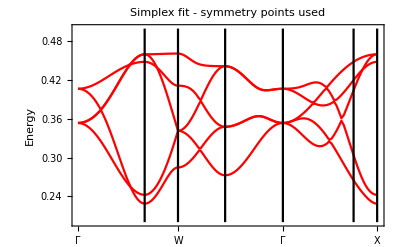

```mathematica
kp=GTBZPath["fcc"];
simp2=GTBandStructure[hfccp,kp,30,5, Joined->True,PlotStyle->Red,PlotRange->{{0,4.5},{.2,.5}},PlotLabel->"Simplex fit - symmetry points used"]
```

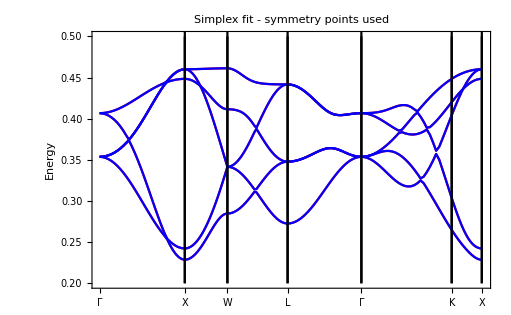

```mathematica
Show[simp2,plt1]
```